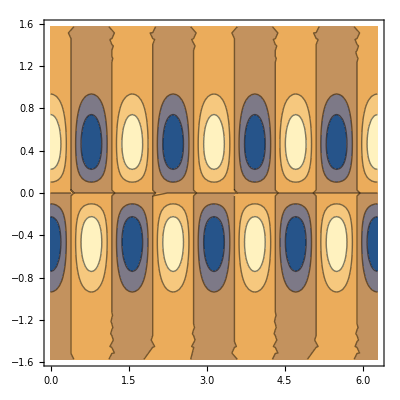

```mathematica
psi[lam_,th_,nn_,mm_]:=LegendreP[nn,mm,Sin[th]]Cos[mm lam]/945;
ContourPlot[psi[lam,th,5,4],{lam,0,2Pi},{th,-Pi/2,Pi/2}]
```

```mathematica
lap=D[Cos[th]D[psi[lam,th,5,4],th],th]/Cos[th]  + D[psi[lam,th,5,4],{lam,2}]/Cos[th]^2
```

Sec[th] (-Sin[th] (4 Cos[4 lam] Cos[th] Sin[th]^2 (-1+Sin[th]^2)+Cos[4 lam] Cos[th] (-1+Sin[th]^2)^2)+Cos[th] (8 Cos[4 lam] Cos[th]^2 Sin[th]^3+12 Cos[4 lam] Cos[th]^2 Sin[th] (-1+Sin[th]^2)-4 Cos[4 lam] Sin[th]^3 (-1+Sin[th]^2)-Cos[4 lam] Sin[th] (-1+Sin[th]^2)^2))-16 Cos[4 lam] Sec[th] (-1+Sin[th]^2)^2 Tan[th]

```mathematica
Simplify[lap]
Simplify[ psi[lam,th,5,4]]
```

-30 Cos[4 lam] Cos[th]^4 Sin[th]

Cos[4 lam] Cos[th]^4 Sin[th]

```mathematica
vrh = -D[psi[lam,th,5,4],lam]/Cos[th]
urh = D[psi[lam,th,5,4],th]
```

4 Sin[4 lam] (-1+Sin[th]^2)^2 Tan[th]

4 Cos[4 lam] Cos[th] Sin[th]^2 (-1+Sin[th]^2)+Cos[4 lam] Cos[th] (-1+Sin[th]^2)^2

```mathematica
Simplify[urh]
```

1/2 Cos[4 lam] Cos[th]^3 (-3+5 Cos[2 th])

```mathematica
Simplify[vrh]
```

4 Cos[th]^3 Sin[4 lam] Sin[th]

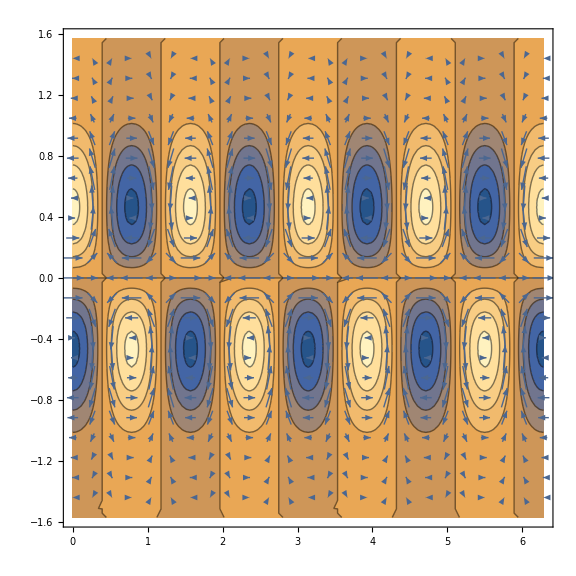

```mathematica
vp=VectorPlot[{Cos[4lam]Cos[th]^3(5Cos[2th]-3),4Cos[th]^3Sin[th]Sin[4lam]},{lam,0,2Pi},{th,-Pi/2,Pi/2},VectorPoints->Fine,Frame->{{0,2Pi},{-Pi/2,Pi/2}},AspectRatio->1/2];
zp = ContourPlot[30psi[lam,th,5,4],{lam,0,2Pi},{th,-Pi/2,Pi/2}];
Show[zp, vp,ImageSize->Large]
```

```mathematica
testHarm[lam_,the_]:=Sin[the](Sin[the]^2-1)^2Cos[4lam];
zG[lam,the] =Simplify[ D[testHarm[lam,the],lam]/Cos[the]]
mG[lam,the] = Simplify[D[testHarm[lam,the],the]]
```

-4 Cos[the]^3 Sin[4 lam] Sin[the]

1/2 Cos[4 lam] Cos[the]^3 (-3+5 Cos[2 the])

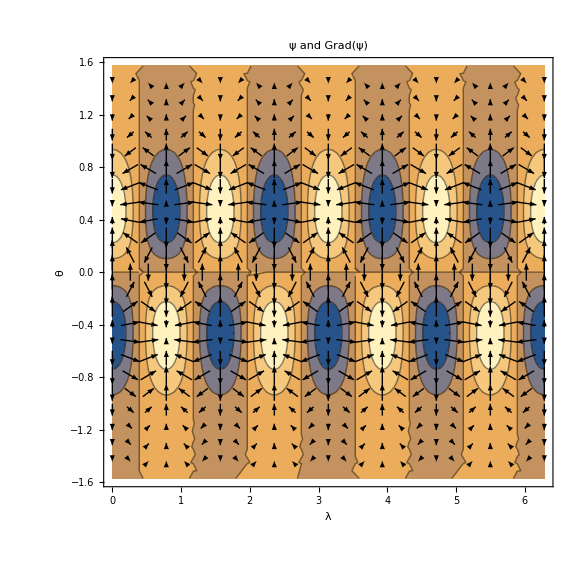

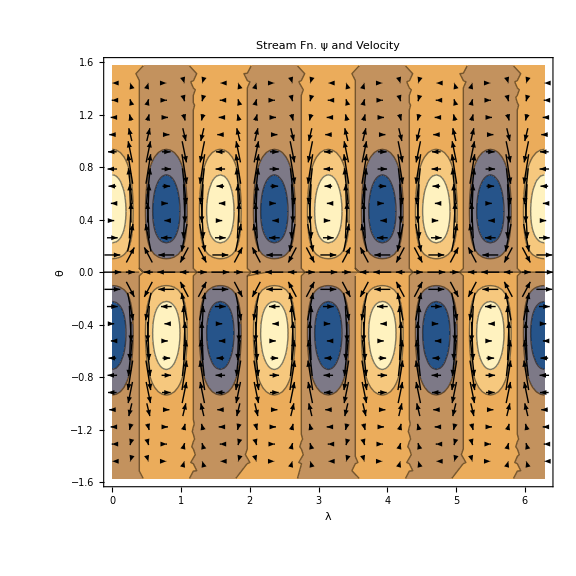

```mathematica
cp = ContourPlot[testHarm[lam,the],{lam,0,2Pi},{the,-Pi/2,Pi/2}];
vpg =VectorPlot[{-4Cos[the]^3Sin[4lam]Sin[the], Cos[4lam]Cos[the]^3(-3+5Cos[2the])/2},{lam,0,2Pi},{the,-Pi/2,Pi/2},VectorPoints->Fine, VectorStyle->Black,PlotLabel->"Gradient ψ",ImageSize->Large];
vpu = VectorPlot[{Cos[4lam]Cos[the]^3(-3+5Cos[2the])/2,4Cos[the]^3Sin[4lam]Sin[the]},{lam,0,2Pi},{the,-Pi/2,Pi/2},VectorPoints->Fine, VectorStyle->Black,PlotLabel->"Velocity", ImageSize->Large];
Show[cp, vpg, PlotLabel->"ψ and Grad(ψ)",FrameLabel->{λ,θ}]
Show[cp, vpu, PlotLabel->"Stream Fn. ψ and Velocity",FrameLabel->{λ,θ}]
```